#### GHZ Graph State Protocol

1. Start with out initial cluster state
2. Do a series of projective measurements in the X and Z bases:





The projective measurement using Hz ensures that all the k values are the same (key for a GHZ state), since that is the ground state eigenvalue. H1-H4 do the same thing in the x-basis ?

3. We calculate the fidelity

#### Preliminary Components

```mathematica
Np = 5; (* Np = Max number of particles (conserved) in each subsystem*)

(*Pauli basis matrices:*)
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
(*Sy=Table[I*KroneckerDelta[i+1,j]*Sqrt[(i+1)*(Np-i)]-I*KroneckerDelta[i,j+1]*Sqrt[(j+1)*(Np-j)],{i,0,Np},{j,0,Np}];*) (*This is my version*)
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];

(*Rotation matrices:
Note that we are using M=3 systems here, hence the dimensions*)
Urotzx1=MatrixExp[I*Sy*Pi/4];
Urotzx=KroneckerProduct[Urotzx1,Urotzx1,Urotzx1]; 
Urotxz=ConjugateTranspose[Urotzx];
Idbig=KroneckerProduct[Id,Id,Id];

(*Exact GHZ state used to calculate fidelity later on:*)
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]; (*Note: Np+1 here because 0 is allowed*)
ghzstate=N[Normalize[ghzstate]];

(*Initial psi cluster state*)
(*Binomial coefficients*)
psi0[k1_,k2_,k3_]=(1/Sqrt[2]^(3*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]];
(*psi1[k1_,k2_,k3_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2]*(1/Sqrt[2]^(Np))*Sqrt[Binomial[Np,k3]]; *)(*Not sure where psi1 comes from*)
(*Creating \psi*)
(*psivec0=ArrayReshape[Table[psi1[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];*) (*This psi is not used?*)
```

#### Performing the Protocol

print[Fidelity Plot 1:]

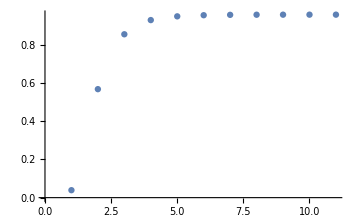

```mathematica
t = 10.0; (*Time*)
nrounds = 10; (*Iterations of the protocol*)


(*Projection Matrices*)
Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id]+KroneckerProduct[Sz,Id,Sz]+KroneckerProduct[Id,Sz,Sz]);
Hamx1=MatrixPower[(-KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig),2];
Hamx2=(-KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx3=(KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx4=(KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;

projmatx[1]=Urotzx.MatrixExp[-Hamx1*t].Urotxz; (*Conjugating by Urot in order to go from z basis to x basis*)
projmatx[2]=Urotzx.MatrixExp[-Hamx2*t].Urotxz;
projmatx[3]=Urotzx.MatrixExp[-Hamx3*t].Urotxz;
projmatx[4]=Urotzx.MatrixExp[-Hamx4*t].Urotxz;
projmatz=MatrixExp[-Hamz*t];

psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];

fidlist={Abs[Conjugate[ghzstate].psi]^2};

(*Going through the iterations*)
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx[Mod[n,4]+1].psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
p1=ListPlot[fidlist];
print["Fidelity Plot 1:"]
Print[p1];
```

#### Repeat the Protocol for M=4 Systems Now

```mathematica
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]]; 
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_,k4_]=(1/Sqrt[2]^(4*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]*Binomial[Np,k4]];
Urotzx1=MatrixExp[I*Sy*Pi/4];
Urotzx=KroneckerProduct[Urotzx1,Urotzx1,Urotzx1,Urotzx1]; 
Urotxz=ConjugateTranspose[Urotzx];
Idbig=KroneckerProduct[Id,Id,Id,Id];
Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id,Id]+KroneckerProduct[Id,Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id,Id]+KroneckerProduct[Sz,Id,Sz,Id]+KroneckerProduct[Sz,Id,Id,Sz]+KroneckerProduct[Id,Sz,Sz,Id]+KroneckerProduct[Id,Sz,Id,Sz]+KroneckerProduct[Id,Id,Sz,Sz]);
Hamx1=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]+KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx2=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]+KroneckerProduct[Id,Id,Sz,Id]-KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx3=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]+KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]-KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx4=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]-KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx5=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]+KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];

t = 15.0; 
nrounds = 20; 
projmatx[1]=Urotzx.MatrixExp[-Hamx1*t].Urotxz; 
projmatx[2]=Urotzx.MatrixExp[-Hamx2*t].Urotxz;
projmatx[3]=Urotzx.MatrixExp[-Hamx3*t].Urotxz;
projmatx[4]=Urotzx.MatrixExp[-Hamx4*t].Urotxz;
projmatx[5]=Urotzx.MatrixExp[-Hamx5*t].Urotxz;
projmatz=MatrixExp[-Hamz*t];

psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]]];

fidlist={Abs[Conjugate[ghzstate].psi]^2};

(*Going through the iterations*)
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx[Mod[n,5]+1].psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
p1=ListPlot[fidlist];
print["Fidelity Plot 2:"]
Show[p1];
```

General::munfl: -9.01861×10^-299+9.01861×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.00128×10^-298-3.00128×10^-298 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.58731×10^-298+2.58731×10^-298 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

print[Fidelity Plot 2:]

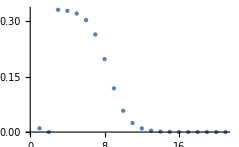
```mathematica
print[-Graphics-](*Doesn't seem to work*)
```

General::munfl: (1.0065×10^-305)/1024 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(1.0065×10^-305)/1024 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.25812×10^-306)/512 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

print[Fidelity Plot 3:]

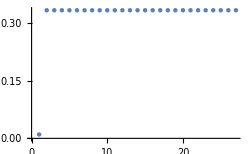
print[-Graphics-]

```mathematica
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]]; 
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_,k4_]=(1/Sqrt[2]^(4*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]*Binomial[Np,k4]];
Urotzx1=MatrixExp[I*Sy*Pi/4];
Urotzx=KroneckerProduct[Urotzx1,Urotzx1,Urotzx1,Urotzx1]; 
Urotxz=ConjugateTranspose[Urotzx];
Idbig=KroneckerProduct[Id,Id,Id,Id];
Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id,Id]+KroneckerProduct[Id,Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id,Id]+KroneckerProduct[Sz,Id,Sz,Id]+KroneckerProduct[Sz,Id,Id,Sz]+KroneckerProduct[Id,Sz,Sz,Id]+KroneckerProduct[Id,Sz,Id,Sz]+KroneckerProduct[Id,Id,Sz,Sz]);
Hamx1=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]+KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx2=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Id,Id,Sz]+KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx3=MatrixPower[(-KroneckerProduct[Id,Id,Id,Sz]-KroneckerProduct[Id,Sz,Id,Id]+KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx4=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]+KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx5=MatrixPower[(-KroneckerProduct[Sz,Id,Id,Id]+KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx6=MatrixPower[(-KroneckerProduct[Id,Id,Id,Sz]+KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx7=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx8=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Sz,Id,Id]-KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx9=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]-KroneckerProduct[Id,Id,Id,Sz]-KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx10=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]+KroneckerProduct[Id,Sz,Id,Id]+KroneckerProduct[Id,Id,Sz,Id]+Np*Idbig),2];
Hamx11=MatrixPower[(KroneckerProduct[Id,Sz,Id,Id]+KroneckerProduct[Id,Id,Sz,Id]+KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx12=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]+KroneckerProduct[Id,Sz,Id,Id]+KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];
Hamx13=MatrixPower[(KroneckerProduct[Sz,Id,Id,Id]+KroneckerProduct[Id,Id,Sz,Id]+KroneckerProduct[Id,Id,Id,Sz]+Np*Idbig),2];

t = 15.0; 
nrounds = 26; 
projmatx[1]=Urotzx.MatrixExp[-Hamx1*t].Urotxz; 
projmatx[2]=Urotzx.MatrixExp[-Hamx2*t].Urotxz;
projmatx[3]=Urotzx.MatrixExp[-Hamx3*t].Urotxz;
projmatx[4]=Urotzx.MatrixExp[-Hamx4*t].Urotxz;
projmatx[5]=Urotzx.MatrixExp[-Hamx5*t].Urotxz;
projmatx[6]=Urotzx.MatrixExp[-Hamx6*t].Urotxz;
projmatx[7]=Urotzx.MatrixExp[-Hamx7*t].Urotxz;
projmatx[8]=Urotzx.MatrixExp[-Hamx8*t].Urotxz;
projmatx[9]=Urotzx.MatrixExp[-Hamx9*t].Urotxz;
projmatx[10]=Urotzx.MatrixExp[-Hamx10*t].Urotxz;
projmatx[11]=Urotzx.MatrixExp[-Hamx11*t].Urotxz;
projmatx[12]=Urotzx.MatrixExp[-Hamx12*t].Urotxz;
projmatx[13]=Urotzx.MatrixExp[-Hamx13*t].Urotxz;
projmatz=MatrixExp[-Hamz*t];

psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]]];

fidlist={Abs[Conjugate[ghzstate].psi]^2};

(*Going through the iterations*)
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx[Mod[n,13]+1].psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
p1=ListPlot[fidlist];
Show["Fidelity Plot 3:"]
print[p1]
```